```mathematica
SDATA={
CI->1.5 10^6,
g-> 9.81,
D1-> 0.750,
D2-> 2 0.750,
d1-> 0.850,
d2-> 0.850,
r1->d1/2,
r2->d2/2,
b1->0.250,
b2->0.250,
h->0.0,
h1->0.8b1,
h2->0.8b2,
m0->212.3,
m1->90.0,
m2->90.0,
Jz0->44.3,
Jz1-> 5.0,
Jz2->5.0,
k-> 5.0 10^6,
kpneu1-> 5.0 10^6,
kpneu2-> 5.0 10^6,
b->2^7 28000.0,
bpneu1->2^7 28000.0,
bpneu2->2^7 28000.0,
IF-> 0.1 6 3400.0/4,
vd-> 2.0,
λ-> 1.0,
vmin->0.0001,
ωmin-> vmin/(d1/2),
vymin-> -1.0 10^-6
};
```

```mathematica
m={m0,m1,m2};
Jz={Jz0,Jz1,Jz2};
M[i_]:={{m⟦i+1⟧,0,0},{0,m⟦i+1⟧,0},{0,0,Jz⟦i+1⟧}};
X={0,D1,-D2};
Y={h,0,0};
Θ={0,θ1[t],θ2[t]};
ξ[t_]={x[t],y[t],α[t],θ1[t],θ2[t]};
q[i_]:={x[t]+Cos[α[t]] X⟦i+1⟧-Sin[α[t]] Y⟦i+1⟧,y[t]+Sin[α[t]] X⟦i+1⟧+Cos[α[t]] Y⟦i+1⟧,α[t] -Θ⟦i+1⟧ };
J[i_]:=D[q[i], {ξ[t]}];
dJ[i_]:=D[J[i], t];
𝕄=Simplify[∑_(i=0)^2 J[i]ᵀ.M[i].J[i]];
𝕧=Simplify[(∑_(i=0)^2 J[i]ᵀ.M[i].dJ[i]).ξ'[t]];
𝕘=Simplify[(∑_(i=0)^2 J[i]ᵀ.{0,m⟦i+1⟧g,0})];
δ1=k/(k+kpneu1)(r1-q[1]⟦2⟧);
δ2=k/(k+kpneu2)(r2-q[2]⟦2⟧);
W1 = π/4  (2 √(δ1(d1-δ1)))b1  (kpneu1((k+kpneu1)/k)δ1+bpneu1 ((k+kpneu1)/k) D[δ1, t]);
W2 = π/4  (2 √(δ2(d2-δ2)))b2  (kpneu2((k+kpneu2)/k)δ2+bpneu2 ((k+kpneu2)/k) D[δ2, t]);

s1 = 1 - D[q[1]⟦1⟧, t]/((r1-δ1) θ1'[t]);
s2 =  ((r2-δ2) θ2'[t])/D[q[2]⟦1⟧, t]-1;
Bn1 =Simplify[ (CI b1 d1)/W1(1+5(δ1/h1))/(1+3(b1 /d1))];
Bn2 =Simplify[ (CI b2 d2)/W2(1+5(δ2/h2))/(1+3(b2 /d2))];
GTR1 = (0.88 (1-Exp[-0.08 Bn1])(1-Exp[-9.5Abs[s1]])+0.032)Tanh[100s1];
GTR2 = (0.88 (1-Exp[-0.08 Bn2])(1-Exp[-9.5Abs[s2]])+0.032)Tanh[100s2];
MRR1=(0.9/Bn1+0.032+(0.5Abs[s1])/(√Bn1))Tanh[100 D[q[1]⟦1⟧, t]];
MRR2=(0.9/Bn2+0.032+(0.5Abs[s2])/(√Bn2))Tanh[100 D[q[2]⟦1⟧, t]];

GT1 = W1 GTR1;
MR1 = W1 MRR1;
GT2 = W2 GTR2;
MR2 = W2 MRR2;
TE = (GT1-MR1+GT2-MR2)/GT1(1-s1);
NTR=(GT1-MR1+GT2-MR2)/(W1+W2);
𝕗0={-IF Tanh[100 x'[t]],0,0};
𝕗1={
W1(GTR1 -MRR1 )Cos[α[t]],
W1 (1+(GTR1 -MRR1  )Sin[α[t]]),
r1 W1 GTR1 
};
𝕗2={
W2(GTR2 -MRR2  )Cos[α[t]],
W2 (1+(GTR2 -MRR2)Sin[α[t]]),
r2 W2 GTR2  
};
𝒻={𝕗0,𝕗1,𝕗2};
𝕗=(∑_(i=0)^2 J[i]ᵀ.𝒻⟦i+1⟧)+{0,0,0,τ[t],0};
```

```mathematica
𝕄//MatrixForm
```

(m0+m1+m2 | 0 | -h m0 Cos[α[t]]+(-D1 m1+D2 m2) Sin[α[t]] | 0 | 0
0 | m0+m1+m2 | (D1 m1-D2 m2) Cos[α[t]]-h m0 Sin[α[t]] | 0 | 0
-h m0 Cos[α[t]]+(-D1 m1+D2 m2) Sin[α[t]] | (D1 m1-D2 m2) Cos[α[t]]-h m0 Sin[α[t]] | Jz0+Jz1+Jz2+h^2 m0+D1^2 m1+D2^2 m2 | -Jz1 | -Jz2
0 | 0 | -Jz1 | Jz1 | 0
0 | 0 | -Jz2 | 0 | Jz2)

```mathematica
𝕧//MatrixForm
```

(-(((D1 m1-D2 m2) Cos[α[t]]-h m0 Sin[α[t]]) α'[t]^2)
-((h m0 Cos[α[t]]+(D1 m1-D2 m2) Sin[α[t]]) α'[t]^2)
0
0
0)

```mathematica
𝕘//MatrixForm
```

(0
g (m0+m1+m2)
g ((D1 m1-D2 m2) Cos[α[t]]-h m0 Sin[α[t]])
0
0)

```mathematica
baux=-(𝕧+𝕘-𝕗)/.τ[t]->𝕄⟦1,1⟧(r1-δ1)(2λ(vd-x'[t])+λ^2(vd t - x[t]))//.{t->0,θ1[0]->0,θ2[0]->0,α[0]->0,x[0]->0,y[0]->r1-0.001,θ1'[0]->ωmin,θ2'[0]->0,α'[0]->0,x'[0]->r1 ωmin,y'[0]->vymin}//.SDATA
```

{-42.2568,-3767.47,616.024,666.176,15.695}

```mathematica
maux=(𝕄/.τ[t]->𝕄⟦1,1⟧(r1-δ1)(2λ(vd-x'[t])+λ^2(vd t - x[t]))//.{t->0,θ1[0]->0,θ2[0]->0,α[0]->0,x[0]->0,y[0]->r1-0.001,θ1'[0]->ωmin,θ2'[0]->0,α'[0]->0,x'[0]->r1 ωmin,y'[0]->vymin}//.SDATA)
```

{{392.3,0,0.,0,0},{0,392.3,-67.5,0,0},{0.,-67.5,307.425,-5.,-5.},{0,0,-5.,5.,0},{0,0,-5.,0,5.}}

```mathematica
LinearSolve[maux,baux]
```

{-0.107715,-9.21245,2.27303,135.508,5.41202}

```mathematica
EQ=(𝕄. ξ''[t]+𝕧+𝕘-𝕗)/.τ[t]->𝕄⟦1,1⟧(r1-δ1)(2λ(vd-x'[t])+λ^2(vd t - x[t]));
sol=NDSolve[{EQ⟦1⟧==0,EQ⟦2⟧==0,EQ⟦3⟧==0,EQ⟦4⟧==0,EQ⟦5⟧==0,θ1[0]==0,θ2[0]==0,α[0]==0,x[0]==0,y[0]==r1-0.013,θ1'[0]==ωmin,θ2'[0]==0,α'[0]==0,x'[0]==r1 ωmin,y'[0]==vymin}//.SDATA,Join[ξ[t],ξ'[t]],{t,0,20},Method->{"EquationSimplification"->"Residual"}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],α[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t],α'[t]→InterpolatingFunction[…][t],θ1'[t]→InterpolatingFunction[…][t],θ2'[t]→InterpolatingFunction[…][t]}}

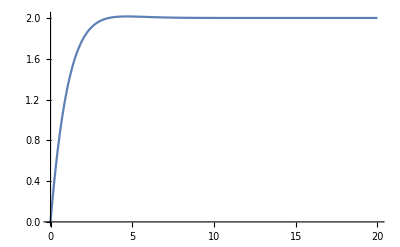

```mathematica
Plot[Evaluate[x'[t]/.sol],{t,0,20},PlotRange->All]
```

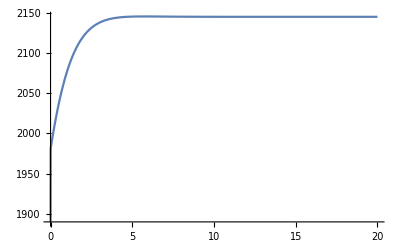

```mathematica
Plot[Evaluate[W1//.SDATA/.sol],{t,0,20},PlotRange->All]
```

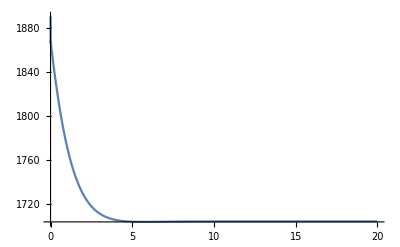

```mathematica
Plot[Evaluate[W2//.SDATA/.sol],{t,0,20},PlotRange->All]
```

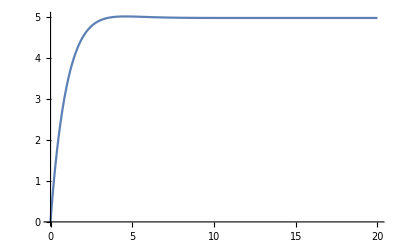

```mathematica
Plot[Evaluate[θ1'[t]/.sol],{t,0,20},PlotRange->All]
```

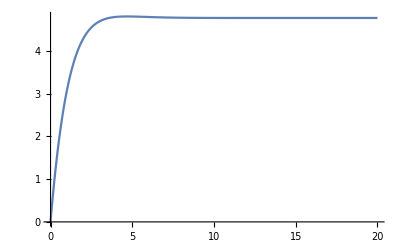

```mathematica
Plot[Evaluate[θ2'[t]/.sol],{t,0,20},PlotRange->All]
```

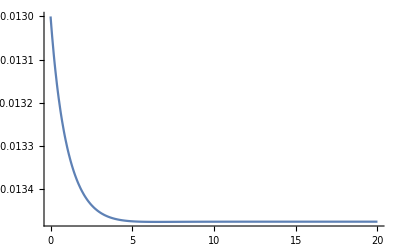

```mathematica
Plot[Evaluate[( y[t]-r1)//.SDATA/.sol],{t,0,20},PlotRange->All]
```

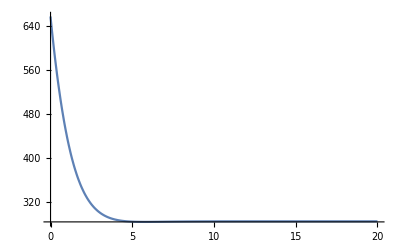

```mathematica
Plot[Evaluate[(𝕄⟦1,1⟧(r1-δ1)(2λ(vd-x'[t])+λ^2(vd t - x[t])))//.SDATA/.sol],{t,0,20},PlotRange->All]
```

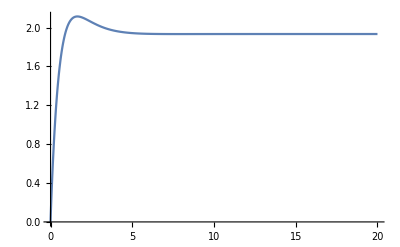

```mathematica
Plot[1/736.499 Evaluate[(θ1'[t](𝕄⟦1,1⟧(r1-δ1)(2λ(vd-x'[t])+λ^2(vd t - x[t]))))//.SDATA/.sol],{t,0,20},PlotRange->All]
```

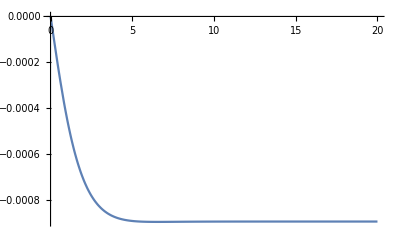

```mathematica
Plot[Evaluate[α[t]/.sol],{t,0,20},PlotRange->All]
```

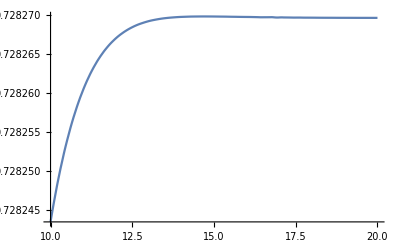

```mathematica
Plot[Evaluate[TE//.SDATA/.sol],{t,10,20},PlotRange->All]
```

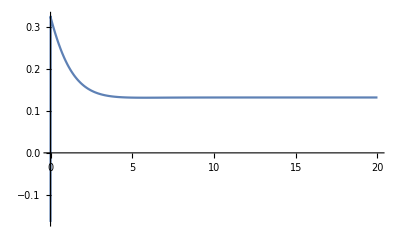

```mathematica
Plot[Evaluate[NTR//.SDATA/.sol],{t,0,20},PlotRange->All]
```

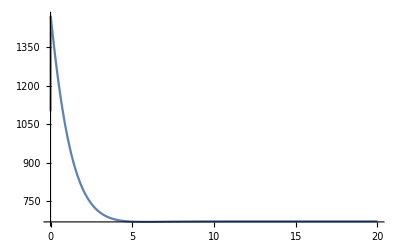

```mathematica
Plot[Evaluate[GT1//.SDATA/.sol],{t,0,20},PlotRange->All]
```

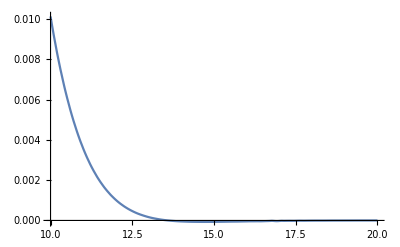

```mathematica
Plot[Evaluate[GT2//.SDATA/.sol],{t,10,20},PlotRange->All]
```

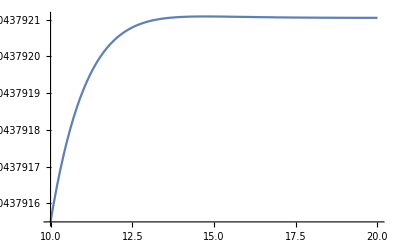

```mathematica
Plot[Evaluate[MRR1//.SDATA/.sol],{t,10,20},PlotRange->All]
```

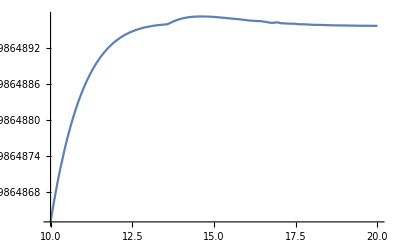

```mathematica
Plot[Evaluate[MRR2//.SDATA/.sol],{t,10,20},PlotRange->All]
```

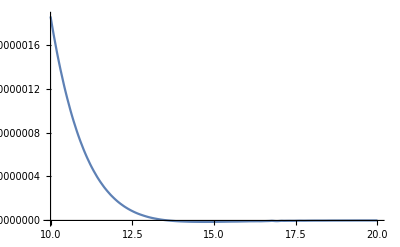

```mathematica
Plot[Evaluate[s2//.SDATA/.sol],{t,10,20},PlotRange->All]
```